```mathematica
SetDirectory[NotebookDirectory[]];
Get["Kimberling.m"]; 
Get["ConicTools.m"];
```

```mathematica
PA={0,0}; PB={Sqrt[3],0}; PC={1,3};
```

```mathematica
(* Calculate ellipses *)
elc = ellipseFociEq[PA[[1]],PA[[2]],PB[[1]],PB[[2]],PC[[1]],PC[[2]]]//Simplify;
elb = ellipseFociEq[PC[[1]],PC[[2]],PA[[1]],PA[[2]],PB[[1]],PB[[2]]]//Simplify;
ela = ellipseFociEq[PB[[1]],PB[[2]],PC[[1]],PC[[2]],PA[[1]],PA[[2]]]//Simplify;
{EA, EB,EC}=ImplicitRegion[matrixToEq[#]==0,{x,y}]&/@{ela,elb,elc};

(* Common chords *)
chorda=NSolve[matrixToEq[elb]==0 &&matrixToEq[elc]==0,{x,y}, Reals]//Simplify;
chordb=NSolve[matrixToEq[ela]==0 &&matrixToEq[elc]==0,{x,y}, Reals]//Simplify;
chordc=NSolve[matrixToEq[ela]==0 &&matrixToEq[elb]==0,{x,y}, Reals]//Simplify;

(* Eq of chords *)
{linea, lineb, linec}=Simplify[lineEq[x/.#[[1]], y/.#[[1]], x/.#[[2]], y/.#[[2]]]&/@{chorda, chordb, chordc}];
```

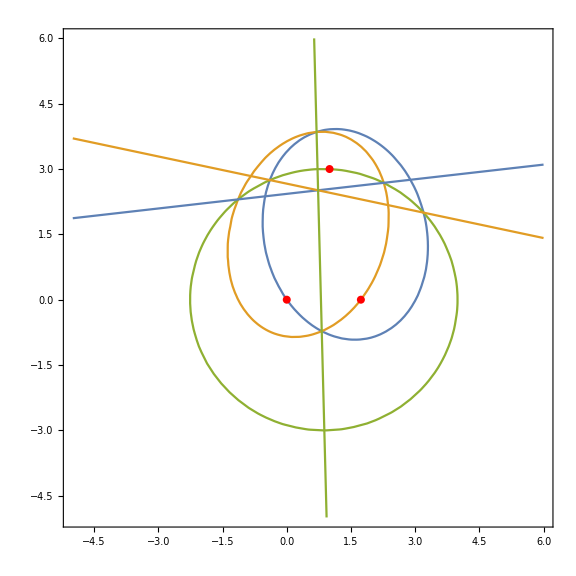

```mathematica
Show[
ContourPlot[{matrixToEq[ela]==0, matrixToEq[elb]==0,matrixToEq[elc]==0} ,
{x,-5,6},{y,-5,6}, 
AspectRatio->Automatic, ImageSize->Large, 
Epilog->{PointSize[0.01],Red,Point[#]&/@{PA, PB, PC}}
]
, ContourPlot[{linea==0, lineb==0, linec==0} ,{x,-5,6},{y,-5,6}]
]
```

```mathematica
(* Check if intersection point is a known Kimberling Center*)
sol=First[SolveValues[linea==0&&lineb==0,{x,y}]];
Table[KimberlingCenter[i,PA,PB,PC]-sol,{i,1,20}]//N
```

{{0.171101,-1.86101},{0.178633,-1.51197},{0.133975,-1.13397},{0.267949,-2.26795},{0.200962,-1.70096},{0.169644,-2.1126},{0.186654,-2.03018},{0.193697,-0.813876},{0.174622,-1.25286},{0.182399,-1.33744},{0.0517101,-2.50092},{0.184372,-1.78988},{0.193466,-2.01374},{-0.0432444,-2.99614},{0.153805,-1.67804},{0.311194,-5.99614},{0.179877,-1.81279},{0.24167,-0.00234719},{0.277505,-2.37188},{-4.44089×10^-16,1.33227×10^-15}}